# PP Elastics Scattering in SHARAQ04

```mathematica
Manipulate[Plot[ArcTan[(2 √(1+a))/(Sin[α Degree]a)] 180/π,{α,0,180},PlotRange->{80,90}],{a,0.01,1}]
```

```mathematica
Manipulate[
Plot[(2(√(1+a))/a)^2/(Sin[θ °]^2 √(Tan[θ °]^2-(2(√(1+a))/a)^2))UnitStep[θ °-ArcTan[2(√(1+a))/a]],{θ,80,90},PlotRange->{All,{0,100}}],{a,0.01,0.173}]
```

```mathematica
(* basic information *)
mp=938.27203;
c=299.792458; (* mm/ns *)
Bρ=2.487;
Bρ2T[m_,Z_,A_,Bρ_]:=1/A( √((Bρ Z c)^2+m^2)-m);
T=Bρ2T[mp,1,1,Bρ];

(* Lornetz *)
γBeam=(mp+T)/mp;
βBeam=√(1-1/γBeam^2);
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],-Sin[θ],0},{0,Sin[θ],Cos[θ],0},{0,0,0,1}}
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,Sin[θ]},{0,0,1,0},{0,-Sin[θ],0,Cos[θ]}}
R[θNN_,ϕNN_,θ_,ϕ_]:=Rz[ϕ].Ry[θ].Rz[-ϕNN].Ry[-θ].Ry[θNN].Rz[-ϕ];
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[ϕ].Ry[θ].Lz[β].Ry[-θ].Rz[-ϕ]
(* Tools *)
KE[A_]:=A[[1]]-mp
Momentum[A_]:=Norm[A[[2;;4]]]
βfromP[A_]:=Momentum[A]/A[[1]]
PolarAngle[A_]:=If[A[[2]]==0 && A[[3]]==0,{0,If[A[[4]]≥ 0,0,π]},{ArcTan[A[[2]],A[[3]]],ArcTan[A[[4]],Norm[A[[2;;3]]]]}] (* ϕ, θ *)
(* detector geometry *)
FL[P_]:=Module[{ang},
ang=PolarAngle[P];
2 1400/(Abs[√3 Cos[ang[[1]]]Sin[ang[[2]]]]+Cos[ang[[2]]])]
ToF[P_]:=FL[P]/(βfromP[P] c)
Accp[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},-1]
(* Deduced Speration energy *)
SpV[P1_,P2_]:=(1-γBeam)mp-γBeam(KE[P1]+KE[P2])+γBeam βBeam (Momentum[P1]Cos[PolarAngle[P1][[2]]]+Momentum[P2]Cos[PolarAngle[P2][[2]]])
Sp[P1_,P2_]:=√((γBeam mp - P1[[1]]-P2[[1]])^2-Momentum[γBeam βBeam mp{0,0,0,1}-P1-P2]^2)

(* 4 momentum vector (E, px, py, pz) *)
PP1[θNN_,ϕNN_]:={1/2 (2 mp+T+T Cos[θNN]),(√(mp T) Cos[ϕNN] Sin[θNN])/(√2),(√(mp T) Sin[θNN] Sin[ϕNN])/(√2),√(T (2 mp+T)) Cos[θNN/2]^2}
PP2[θNN_,ϕNN_]:={1/2 (2 mp+T-T Cos[θNN]),-(√(mp T) Cos[ϕNN] Sin[θNN])/(√2),-(√(mp T) Sin[θNN] Sin[ϕNN])/(√2),√(T (2 mp+T)) Sin[θNN/2]^2}
(* Magnetic Deflection *)
BField=0.064 ;(* T*)
Bradius = 0.11; (* m*)
MagneticDeflected[B_,r_,V_]:=(r B c)/Momentum[V]
```

## General

In Center of Momentum Frame because it is easier to make and use Ay fucntion

```mathematica
Generator[θin_,ϕin_,θ_,ϕ_,BField_,BRadius_]:={
(* 1*)P1i={mp+T,√(2mp T+T^2)Cos[ϕin]Sin[θin],√(2mp T+T^2)Sin[ϕin]Sin[θin],√(2mp T+T^2)Cos[θin] },
P1it=Ry[-θin].Rz[-ϕin].P1i;
(* 2*)P2i={mp,0,0,0},
Pci=1/2(P1it+P2i);
(* 3*)β=βfromP[Pci],
P1ict=Lz[-β].P1it;
P2ict=Lz[-β].P2i;
P1fct=Rz[ϕ].Ry[θ].P1ict;
P2fct=Rz[ϕ].Ry[θ].P2ict;
(* 4*)P1ic=Rz[ϕin].Ry[θin].P1ict,
(* 5*)P2ic=Rz[ϕin].Ry[θin].P2ict,
(* 6*)P1fc=Rz[ϕin].Ry[θin].P1fct,
(* 7*)P2fc=Rz[ϕin].Ry[θin].P2fct,
P1ft=Rz[ϕin].Ry[θin].Lz[β].P1fct;
P2ft=Rz[ϕin].Ry[θin].Lz[β].P2fct;
(* 8*)P1f=Ry[(BField BRadius c)/Momentum[P1ft]].P1ft,
(* 9*)P2f=Ry[(BField BRadius  c)/Momentum[P2ft]].P2ft
}
```

```mathematica
Observable[list_]:=Monitor[Table[{
(*1 ToF 1*)ToF[list[[i,1]]],
(*2 ToF 2*)ToF[list[[i,2]]],
(*3 Angle 1*)PolarAngle[list[[i,1]]],
(*4 Angle 2*)PolarAngle[list[[i,2]]],
(*5 Sp *)Sp[list[[i,1]],list[[i,2]]],
(*6 Δθ *)(PolarAngle[list[[i,1]]][[2]]+PolarAngle[list[[i,2]]][[2]])180/π,
(*7 Δϕ *)If[(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π>90,(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π-180,(PolarAngle[list[[i,1]]][[1]]-PolarAngle[list[[i,2]]][[1]])180/π+180],
(*8 KE 1 *) KE[list[[i,1]]],
(*9 KE 2 *) KE[list[[i,2]]],
(*10 KE1+KE2 *) KE[list[[i,1]]]+KE[list[[i,2]]]
},{i,1,Length[list]}],i];
ObserPlots[olist_,n_]:=Module[{tolist},
tolist=Transpose[olist];
GraphicsGrid[{
{Histogram[{tolist[[1]],tolist[[2]]},{7, 20,0.2},Frame->True,FrameLabel->{"ToF1, ToF2","Counts"},GridLines->Automatic],
Histogram[{Transpose[tolist[[3]]][[2]],Transpose[tolist[[4]]][[2]]},Frame->True,FrameLabel->{"θ1, θ2","Counts"},GridLines->Automatic]
},
{Histogram[tolist[[6]],{85,89,0.1},Frame->True,FrameLabel->{"Δθ","Counts"},GridLines->Automatic],
Histogram[tolist[[7]],Frame->True,FrameLabel->{"Δϕ","Counts"},GridLines->Automatic]
},
{Histogram[{tolist[[8]],tolist[[9]]},Frame->True,FrameLabel->{"T1, T2","Counts"},GridLines->Automatic],
DensityHistogram[Table[{olist[[i,7]],olist[[i,6]]},{i,1,n}],Frame->True,FrameLabel->{"Δϕ","Δθ"},GridLines->Automatic]
},
{Histogram[tolist[[10]],Frame->True,FrameLabel->{"T1+T2","Counts"},GridLines->Automatic],
Histogram[tolist[[5]],Frame->True,FrameLabel->{"Sp","Counts"},GridLines->Automatic]
},
{DensityHistogram[Table[{olist[[i,3,2]] 180/π,olist[[i,1]]},{i,1,n}],{{1},{0.25}},PlotRange->{{20,70},{7,20}},Frame->True,FrameLabel->{"θ1","ToF1"},GridLines->Automatic],
DensityHistogram[Table[{olist[[i,4,2]] 180/π,olist[[i,2]]},{i,1,n}],{{1},{0.25}},PlotRange->{{20,70},{7,20}},Frame->True,FrameLabel->{"θ2","ToF2"},GridLines->Automatic]
}
},ImageSize->800]]
```

```mathematica
Manipulate[
GraphicsGrid[{{
TableForm[Generator[θin °,ϕin °,θ °,ϕ °,B,r]],
Graphics3D[{
Arrow[{{0,0,0},{0,0,1000}}],
Arrow[{{0,0,0},{500,0,0}}],
Arrow[{{0,0,0},{0,500,0}}],
Green,Arrow[{-P1i[[2;;4]],{0,0,0}}],
Red,Arrow[{{0,0,0},P1f[[2;;4]]}],
Blue,Arrow[{{0,0,0},P2f[[2;;4]]}],
Pink,Arrow[{{0,0,0},P1fc[[2;;4]]}],
Cyan,Arrow[{{0,0,0},P2fc[[2;;4]]}]
}]
}},ImageSize->700]
,{{θin,0},-90,90},{{ϕin,0},-180,180},{{θ,90},0,180},{{ϕ,0},-180,180},{B,0,0.064},{r,0,0.5}]
```

### Generate distribution For Polarized Target

```mathematica
(* isotropic distribution and polarized *)
Manipulate[PolarPlot[{1,1+P Sin[2θ]},{θ,0,2π},PlotLabel-> "Cross Section in C.M. Frame"],{P,0,1}]
```

```mathematica
Manipulate[Plot[{Sin[θ],(1+P Sin[2θ])Sin[θ]},{θ,0,π},PlotRange->{0,2}],{P,0,1}]
```

```mathematica
(* to generate the distribution *)
dΩ=σ[θ]Sin[θ]dθ dϕ = d(g[θ]) dϕ
(* thus *)
g[θ]=Integrate[f[θ] Sin[θ],θ]
(* Thus get the g^-1 *)
Solve[2μ-1 == g[θ],θ]
(* g^-1[μ] is the distribution *)
```

```mathematica
Integrate[(1+h Sin[2θ])Sin[θ],θ]
Solve[2 μ-1==-%,θ]
```

-Cos[θ]+1/2 h Sin[θ]-1/6 h Sin[3 θ]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,1]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,1]]},{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,2]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,2]]},{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,3]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,3]]},{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,4]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,4]]},{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,5]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,5]]},{θ→-ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,6]]},{θ→ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,6]]}}

```mathematica
Manipulate[Plot[{
ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,1]],
ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,2]]
},{μ,0,1},PlotStyle->{Red,Blue}],{h,0,1}]
```

```mathematica
Dist[h_,μ_]:=ArcCos[Root[9-4 h^2-36 μ+36 μ^2+(18-36 μ) #1+(9+12 h^2) #1^2-12 h^2 #1^4+4 h^2 #1^6&,2]]
Manipulate[Plot[{Dist[h,μ],ArcCos[2μ-1]},{μ,0,1},PlotStyle->{Red,Blue}],{h,0,1}]
```

### Uniform Distribution

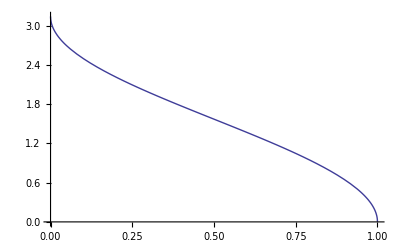

```mathematica
Plot[ArcCos[2 u-1],{u,0,1}]
```

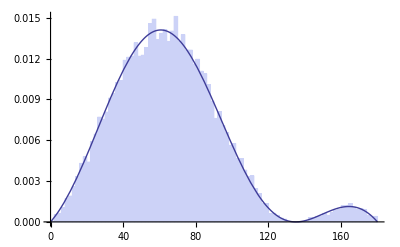

```mathematica
ProbDensity[x_]:=(1+Sin[2x °])Sin[x °]
ProbDist=ProbabilityDistribution[ProbDensity[x],{x,0,180,1}];
nfactor=Sum[Sin[x °],{x,0,180,1}]//N;
Cus=RandomVariate[ProbDist,20000];
Show[
Histogram[Cus,100,"ProbabilityDensity"],
Plot[PDF[ProbDist,x]/nfactor,{x,0,180},PlotStyle->Thick]
]
```

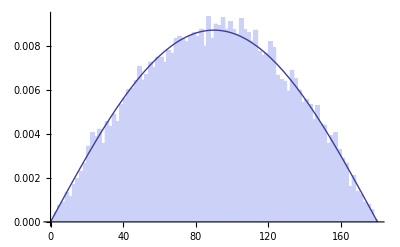

```mathematica
n=20000;
Show[
Histogram[(Table[ArcCos[2 RandomReal[{0,1}]-1],{i,1,n}] 180)/π,100,"ProbabilityDensity"],
Plot[Sin[x °]/nfactor,{x,0,180}]
]
```

## Generate data

```mathematica
nPre=50000;
Pol=0.0;
σ[θ_,ϕ_]:=(1+Pol 0.38Sin[2 θ]Cos[ϕ]) (* cross section in CM frame *)
(* Generate distribution by Selection Method *)
vlist=(* θ,ϕ,r *)Table[{RandomReal[{0,π}],RandomReal[{-π,π}],RandomReal[{0,1.3}]},{i,1,nPre}];
Svlist=
Select[
Table[
If[vlist[[i,3]]>σ[vlist[[i,1]],vlist[[i,2]]]Sin[vlist[[i,1]]],{0,0,0},vlist[[i]]],{i,1,nPre}
],#≠{0,0,0}&];
n=Length[Svlist]
dpoint=Table[vlist[[i,3]]{Cos[vlist[[i,2]]]Sin[vlist[[i,1]]],Sin[vlist[[i,2]]]Sin[vlist[[i,1]]],Cos[vlist[[i,1]]]},{i,1,nPre}];
Sdpoint=Table[Svlist[[i,3]]{Cos[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Sin[Svlist[[i,2]]]Sin[Svlist[[i,1]]],Cos[Svlist[[i,1]]]},{i,1,n}];
GraphicsGrid[{{
SphericalPlot3D[{σ[θ,ϕ],σ[θ,ϕ]Sin[θ]},{θ,0,π},{ϕ,-π,π},PlotStyle->{Directive[Opacity[0.5],Red],Directive[Opacity[0.5],Blue]}],
Graphics3D[{
Blue,
Arrow[{{0,0,0},{0,0,1.5}}],
Arrow[{{0,0,0},{1.5,0,0}}],
Black,PointSize[Small],Point[dpoint],
Red,Point[Sdpoint]
}]}},ImageSize-> 800]
```

24641

-Graphics-

```mathematica
θList=Table[Svlist[[i,1]],{i,1,n}];
ϕList=Table[Svlist[[i,2]],{i,1,n}];
(*GraphicsGrid[{{Histogram[θList,Automatic,"PDF"],,Histogram[ϕList,Automatic,"PDF"]}},ImageSize->800]*)
(*DensityHistogram[Table[{θList[[i]],ϕList[[i]]},{i,1,n}],{{0.1},{0.1}},ImageSize->500]*)
θinList=Table[ RandomReal[{-0.03,0.03}],{i,1,n}];
ϕinList=Table[  RandomReal[{-0.04,0.06}],{i,1,n}];
P4List=Monitor[Table[Generator[θinList[[i]],ϕinList[[i]],θList[[i]],ϕList[[i]],0.064,0.11][[8;;9]],{i,1,n}],i];
(* Rearrange Data *)
ArrgP4List=Monitor[Table[
If[π/2≥ PolarAngle[P4List[[i,1]]][[1]]≥ -π/2,P4List[[i]],{P4List[[i,2]],P4List[[i,1]]}]
,{i,1,n}],i];
```

```mathematica
P4Obser=Observable[ArrgP4List];
```

```mathematica
ObserPlots[P4Obser,n]
```

$Aborted

```mathematica
(* skiping Multi scattering *)
MSData=ArrgP4List;
MSObserv=P4Obser;
```

## Detector Acceptance

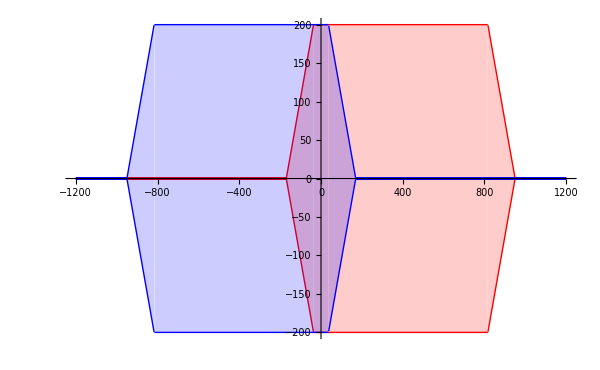

```mathematica
(* for reducing the event number that is outside of the detector *)
Rotate[
Show[
Plot[{Accp[x],-Accp[x]},{x,-1200,1200},PlotStyle->{Red},ImageSize->600,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Red]],
Plot[{Accp[-x],-Accp[-x]},{x,-1200,1200},PlotStyle->{Blue},ImageSize->600,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.2],Blue]]
],π]
```

```mathematica
Rot1=RotationMatrix[60°,{0,-1,0}];
Rot2=RotationMatrix[60°,{0,1,0}];
```

```mathematica
(* Project the ray on the MWDC plane *)
ProjXY1=Table[1022.37/({(√3)/2,0,1/2}.Normalize[ArrgP4List[[i,1]][[2;;4]]])Normalize[ArrgP4List[[i,1]][[2;;4]]],{i,1,n}];
ProjXY2=Table[1022.37/({-(√3)/2,0,1/2}.Normalize[ArrgP4List[[i,2]][[2;;4]]])Normalize[ArrgP4List[[i,2]][[2;;4]]],{i,1,n}];
(* Rotate *)
RotProjXY1=Table[Rot1.ProjXY1[[i]],{i,1,n}];
RotProjXY2=Table[Rot2.ProjXY2[[i]],{i,1,n}];
(* Filter events by MWDC detection area , Filter will select MWDC pos and ToF*)
AccpXY=Select[
Table[
If[Accp[-RotProjXY1[[i,1]]]>Abs[RotProjXY1[[i,2]]] && Accp[RotProjXY2[[i,1]]]>Abs[RotProjXY2[[i,2]]],
{RotProjXY1[[i]],RotProjXY2[[i]]},{{0,0,0},{0,0,0}}],{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
AccpP4List=Select[
Table[
If[Accp[-RotProjXY1[[i,1]]]>Abs[RotProjXY1[[i,2]]] && Accp[RotProjXY2[[i,1]]]>Abs[RotProjXY2[[i,2]]],ArrgP4List[[i]],{{0,0,0},{0,0,0}}],{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
m=Length[AccpXY]
```

2661

```mathematica
test1=Table[ArrgP4List[[i,1]][[2;;4]],{i,1,n}];
test2=Table[ArrgP4List[[i,2]][[2;;4]],{i,1,n}];
a1=Table[Rot2.AccpXY[[i,1]],{i,1,m}];
a2=Table[Rot1.AccpXY[[i,2]],{i,1,m}];
draw=Table[{Hue[(PolarAngle[Join[{1},a1[[i]]]][[2]])/π],Point[{a1[[i]],a2[[i]]}]},{i,1,m}];
Graphics3D[{
Arrow[{{0,0,0},{0,0,1000}}],
Arrow[{{0,0,0},{0,500,0}}],
Arrow[{{0,0,0},Rot2.{0,0,1000}}],
Arrow[{{0,0,0},Rot1.{0,0,1000}}],
PointSize[Small],Cyan,Point[test1],
Blue,Point[test2],
draw
},ImageSize->600]
```

-Graphics3D-

```mathematica
AccpP4Obser=Observable[AccpP4List];
```

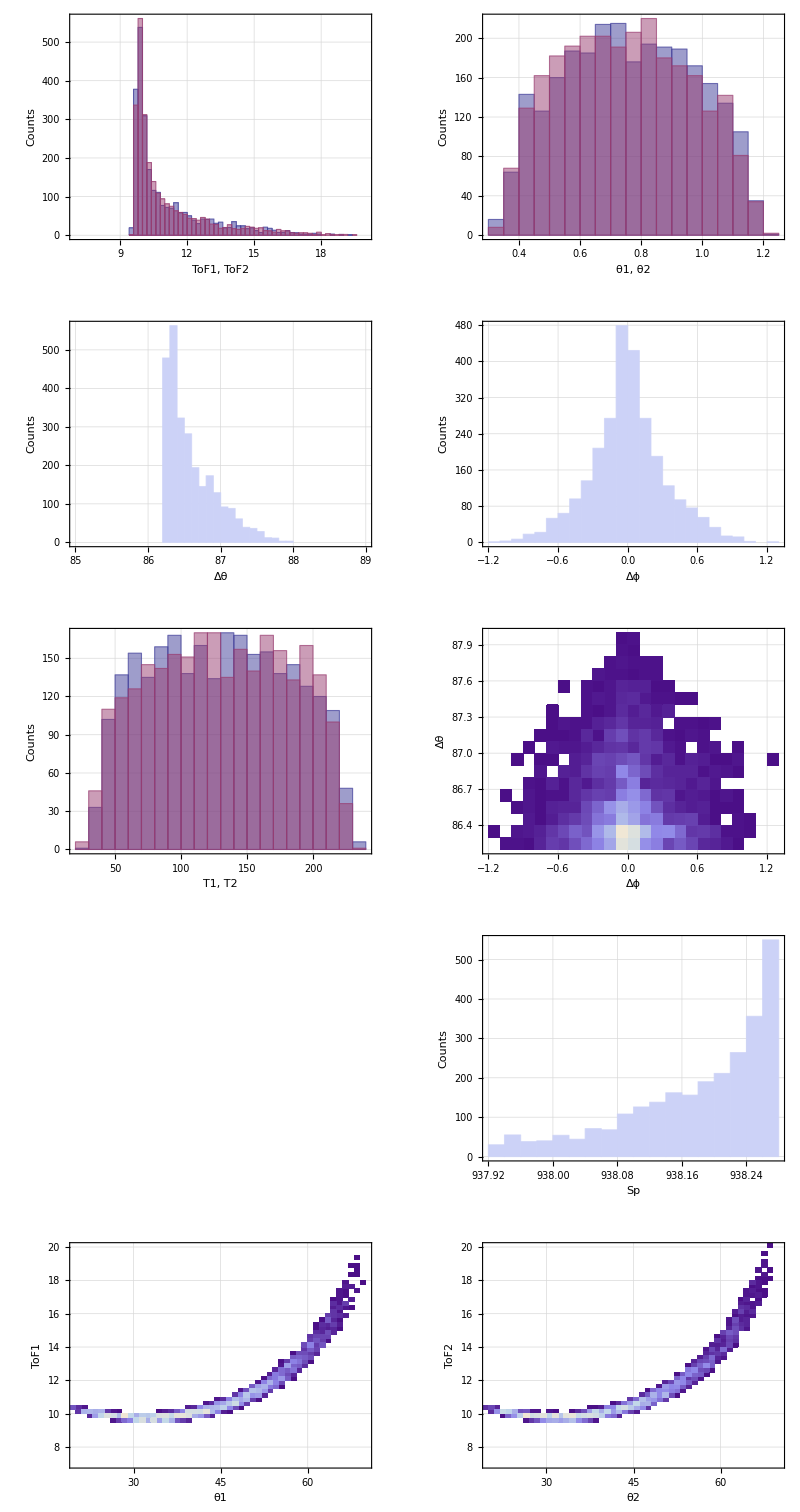

```mathematica
ObserPlots[AccpP4Obser,m]
```

## Multi-Scattering

```mathematica
ScatV[V_,ΔE_,σΔE_,Δθ_]:=Module[{newE,newk,orgP,oldθ,oldϕ,newP},
newE=KE[V]-ΔE+RandomVariate[NormalDistribution[0,σΔE]];
newk=√(2mp newE+newE^2);
orgP=Normalize[V[[2;;4]]];
{oldϕ,oldθ}=PolarAngle[V];
newP=Drop[R[Δθ,RandomReal[{0,2π}],oldθ,oldϕ].Join[{0},orgP],{1}];
Join[{mp+newE},newk newP]]
```

```mathematica
CrystalThickness=1000; (*μm*)
path[depth_,θ_]:=(CrystalThickness - depth)/Cos[θ]
```

```mathematica
MultiCrystal={
(* energy [MeV], thickness[μm], ΔE,Estraggling, θstraggling [mrad],Lateral spread [μm]*)
{{20,50,0.16357,0.021696,3.0681,0.015202},
{20,100,0.3284,0.030806,4.3568,0.043284},
{20,300,0.99982,0.054199,7.6748,0.23034},
{20,500,1.6917,0.071151,10.085,0.50851},
{20,700,2.4059,0.085747,12.158,0.86669},
{20,1000,3.5262,0.10582,14.973,1.5513},
{20,1500,5.5524,0.13882,19.407,3.1579},
{20,2000,7.8559, 0.17713,24,6.0001},
{20,2500,10.607,0.23303,25.63,9.6776},
{20,3000,14.3,0.36084,25.925,7.6602}
},
{{50,50,0.077627,0.021721,1.2418,0.0061349},
{50, 100,0.15537,0.030741,1.7576,0.017375},
{50,300,0.46743,0.053399,3.0535,0.090756},
{50,500,0.78128,0.069138,3.9542,0.19628},
{50,700,1.0969,0.082045,4.6933,0.32679},
{50,1000,1.5737,0.098494,5.636,0.56215},
{50,1500,2.3772,0.12153,6.9582,1.0434},
{50,2000,3.19,0.14125,8.1004,1.6258},
{50,2500,4.0145,0.15909,9.1325,2.2996},
{50,3000,4.8522,0.17568,10.09,3.061}
},
{{80,50,0.053681,0.021993,0.78711,0.0038867},
{80,100,0.10739,0.031112,1.1135,0.011},
{80,300,0.32257,0.053951,1.9311,0.057284},
{80,500,0.53826,0.069733,2.4963,0.12353},
{80,700,0.75446,0.082607,2.9576,0.20509},
{80,1000,1.0797,0.09891,3.5419,0.35134},
{80,1500,1.6245,0.1215,4.3523,0.64897},
{80,2000,2.1725,0.14071,5.0424,1.0045},
{80,2500,2.7238,0.15779,5.6566,1.4112},
{80,3000,3.2782,0.17337,6.2176,1.8629}
},
{{100,50,0.045373,0.022216,0.63548,0.0031417},
{100, 100,0.090763,0.031424,0.89891,0.0088893},
{100,300,0.2725,0.054469,1.5583,0.046256},
{100,500,0.45451,0.070371,2.0135,0.099668},
{100,700,0.63679,0.083326,2.3845,0.16533},
{100,1000,0.91074,0.099704,2.8538,0.2829},
{100,1500,1.3687,0.12234,3.5028,0.52153},
{100,2000,1.8285,0.14152,4.0537,0.80573},
{100,2500,2.2899,0.15852,4.5422,1.1299},
{100,3000,2.7531,0.17397,4.9869,1.4903}
},
{{120,50,0.039681,0.022452,0.53433,0.0026431},
{120,100,0.079372,0.031756,0.75578,0.0074776},
{120,300,0.23824,0.05503,1.3099,0.038893},
{120,500,0.39728,0.071079,1.6921,0.083768},
{120,700,0.55648,0.084144,2.0034,0.1389},
{120,1000,0.7956,0.10065,2.3752,1.6274},
{120,1500,1.195,0.12342,2.9401,0.43741},
{120,2000,1.5955,0.14269,3.4003,0.67508},
{120,2500,1.997,0.15973,3.8077,0.94573},
{120,3000,2.3995,0.1752,4.1778,1.2462}
},
{{150,50,0.033866,0.022803,0.43305,0.0021429},
{150,100,0.067738,0.03225,0.61249,0.006062},
{150,300,0.20328,0.055876,1.0613,0.031519},
{150,500,0.33892,0.072158,1.3707,0.0067863},
{150,700,0.47465,0.085404,1.6226,0.11249},
{150,1000,0.67841,0.10212,1.9406,0.19225},
{150,1500,1.0185,0.12517,2.3792,0.35376},
{150,2000,1.3592,0.14464,2.7502,0.54552},
{150,2500,1.7004,0.16184,3.0781,0.7636},
{150,3000,2.0422,0.17742,3.3756,1.0054}
},
{{170,50,0.03108,0.023042,0.38531,0.0019069},
{170,100,0.062163,0.032588,0.54496,0.0053942},
{170,300,0.18654,0.056457,0.94422,0.028044},
{170,500,0.31098,0.072902,1.2194,0.060371},
{170,700,0.43548,0.086279,1.4433,0.10006},
{170,1000,0.62237,0.10316,1.726,0.17097},
{170,1500,0.93416,0.12642,2.1157,0.3145},
{170,2000,1.2464,0.14605,2.4451,0.48481},
{170,2500,1.5591,0.16339,2.736,0.67841},
{170,3000,1.8721,0.17909,2.9997,0.89291}
},
{{200,50,0.027908,0.023394,0.33151,0.0016408},
{200,100,0.055819,0.033086,0.46886,0.0046414},
{200,300,0.16749,0.057316,0.8123,0.024126},
{200,500,0.2792,0.074006,1.0489,0.051931},
{200,700,0.39095,0.087579,1.2414,0.086057},
{200,1000,0.55866,0.1047,1.4844,0.14702},
{200,1500,0.83839,0.12829,1.8192,0.27036},
{200,2000,1.1184,0.14818,2.102,0.41663},
{200,2500,1.3987,0.16574,2.3516,0.58281},
{200,3000,1.6792,0.18163,2.5777,0.76685}
},
{{230,50,0.025529,0.02374,0.29165,0.0014427},
{230,100,0.051061,0.033575,0.41248,0.004081},
{230,300,0.15321,0.058161,0.71458,0.021212},
{230,500,0.25538,0.075095,0.9227,0.0045656},
{230,700,0.35759,0.088865,1.092,0.075653},
{230,1000,0.51095,0.10623,1.3056,0.12924},
{230,1500,0.76672,0.13015,1.5998,0.23761},
{230,2000,1.0227,0.15033,1.8482,0.36611},
{230,2500,1.2789,0.16812,2.0674,0.51205},
{230,3000,1.5353,0.18423,2.2659,0.67364}
},
{{260,50,0.0237,0.024114,0.26091,0.0012909},
{260,100,0.047401,0.034103,0.36899,0.0036515},
{260,300,0.14222,0.059074,0.63922,0.018979},
{260,500,0.23706,0.076272,0.82536,0.040846},
{260,700,0.33192,0.090254,0.97674,0.067678},
{260,1000,0.47426,0.10789,1.1677,0.1156},
{260,1500,0.7116,0.13217,1.4307,0.21251},
{260,2000,0.94913,0.15264,1.6528,0.32738},
{260,2500,1.1868,0.1707,1.8486,0.45782},
{260,3000,1.4245,0.18704,2.0259,0.6022}
}
};
Dimensions[MultiCrystal]
```

{10,10,6}

```mathematica
ΔECrystal=Interpolation[Flatten[MultiCrystal[[1;;10,1;;10,{1,2,3}]],1]];
EstrCrystal=Interpolation[Flatten[MultiCrystal[[1;;10,1;;10,{1,2,4}]],1]];
θstrCrystal=Interpolation[Flatten[MultiCrystal[[1;;10,1;;10,{1,2,5}]],1]];
```

```mathematica
MSCrystalP4List=Monitor[Table[
{ScatV[AccpP4List[[i,1]],
ΔECrystal[AccpP4Obser[[i,8]],path[RandomReal[{0,950}],AccpP4Obser[[i,3,2]]]],
EstrCrystal[AccpP4Obser[[i,8]],path[RandomReal[{0,950}],AccpP4Obser[[i,3,2]]]],
θstrCrystal[AccpP4Obser[[i,8]],path[RandomReal[{0,950}],AccpP4Obser[[i,3,2]]]]/1000
],
ScatV[AccpP4List[[i,2]],
ΔECrystal[AccpP4Obser[[i,9]],path[RandomReal[{0,950}],AccpP4Obser[[i,4,2]]]],
EstrCrystal[AccpP4Obser[[i,9]],path[RandomReal[{0,950}],AccpP4Obser[[i,4,2]]]],
θstrCrystal[AccpP4Obser[[i,9]],path[RandomReal[{0,950}],AccpP4Obser[[i,4,2]]]]/1000
]
},{i,1,m}],i];
```

```mathematica
MSCrystalP4Obser=Observable[MSCrystalP4List];
```

```mathematica
AccpP4List[[1]]
MSCrystalP4List[[1]]
```

{{1140.37,284.307,48.838,580.415},{996.335,-287.528,-48.7704,165.162}}

{{1139.87,284.559,49.1187,579.279},{995.829,-286.799,-48.4286,163.471}}

```mathematica
MSCrystalP4Obser[[1,{4,9}]]
```

{{-2.97431,1.05877},57.5573}

```mathematica
dotproduct (*mrad*)=Table[ArcCos[(AccpP4List[[i,1,2;;4]].MSCrystalP4List[[i,1,2;;4]])/(Norm[AccpP4List[[i,1,2;;4]]]Norm[MSCrystalP4List[[i,1,2;;4]]])]1000,{i,1,m}];
```

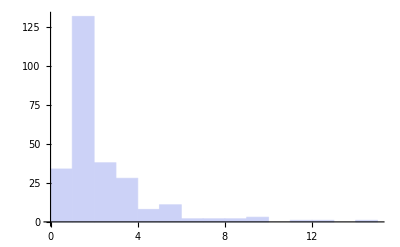

```mathematica
Histogram[dotproduct]
```

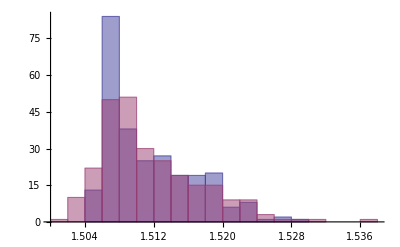

```mathematica
Histogram[
{Table[AccpP4Obser[[i,3,2]]+AccpP4Obser[[i,4,2]],{i,1,m}],
Table[MSCrystalP4Obser[[i,3,2]]+MSCrystalP4Obser[[i,4,2]],{i,1,m}]}]
```

```mathematica
(* 256um Kapton, 2m Air, 100um Maylar *)
ΔEAir=Interpolation[{
{10,11},
{20,7},
{25.0,6.00695},
{27.1,5.56307},
{30,5.07539},
{35,4.42979},
{40,3.94807},
{50,3.27243},
{60,2.81484},
{80,2.24327},
{100,1.892473},
{120,1.653914},
{140,1.480981},
{160,1.349884},
{180,1.246814},
{200,1.163668},
{220,1.09489},
{225.9,1.07786},
{240,1.037775},
{250,1.012578},
{260,0.989286}
}];
θstrCrystal (* mrad *)=Interpolation[{
{25.0,28.66},
{27.1,26.18},
{30,23.42},
{35,19.88},
{40,17.30},
{50,13.77},
{60,11.48},
{80,8.64},
{100,6.96},
{120,5.85},
{140,5.05},
{160,4.45},
{180,3.99},
{200,3.62},
{220,3.32},
{225.9,3.24},
{240,3.06},
{250,2.95},
{260,2.85}
}];
```

```mathematica
MSData=Monitor[Table[
{ScatV[AccpP4List[[i,1]],ScatSpread[KE[AccpP4List[[i,1]]]],EngLost[KE[AccpP4List[[i,1]]]]],
ScatV[AccpP4List[[i,2]],ScatSpread[KE[AccpP4List[[i,2]]]],EngLost[KE[AccpP4List[[i,2]]]]]
},{i,1,m}],i];
```

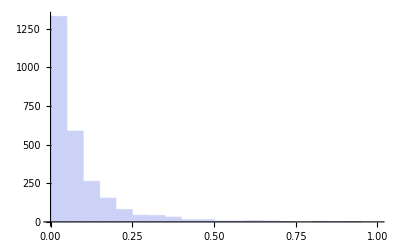

```mathematica
(*Compare the angle CHange *)
Histogram[
Table[ArcCos[Normalize[MSData[[i,1]][[2;;4]]].Normalize[AccpP4List[[i,1]][[2;;4]]]] 180/π,{i,1,m}],{0,1,0.05}
]
```

```mathematica
MSObserv=Observable[MSData];
```

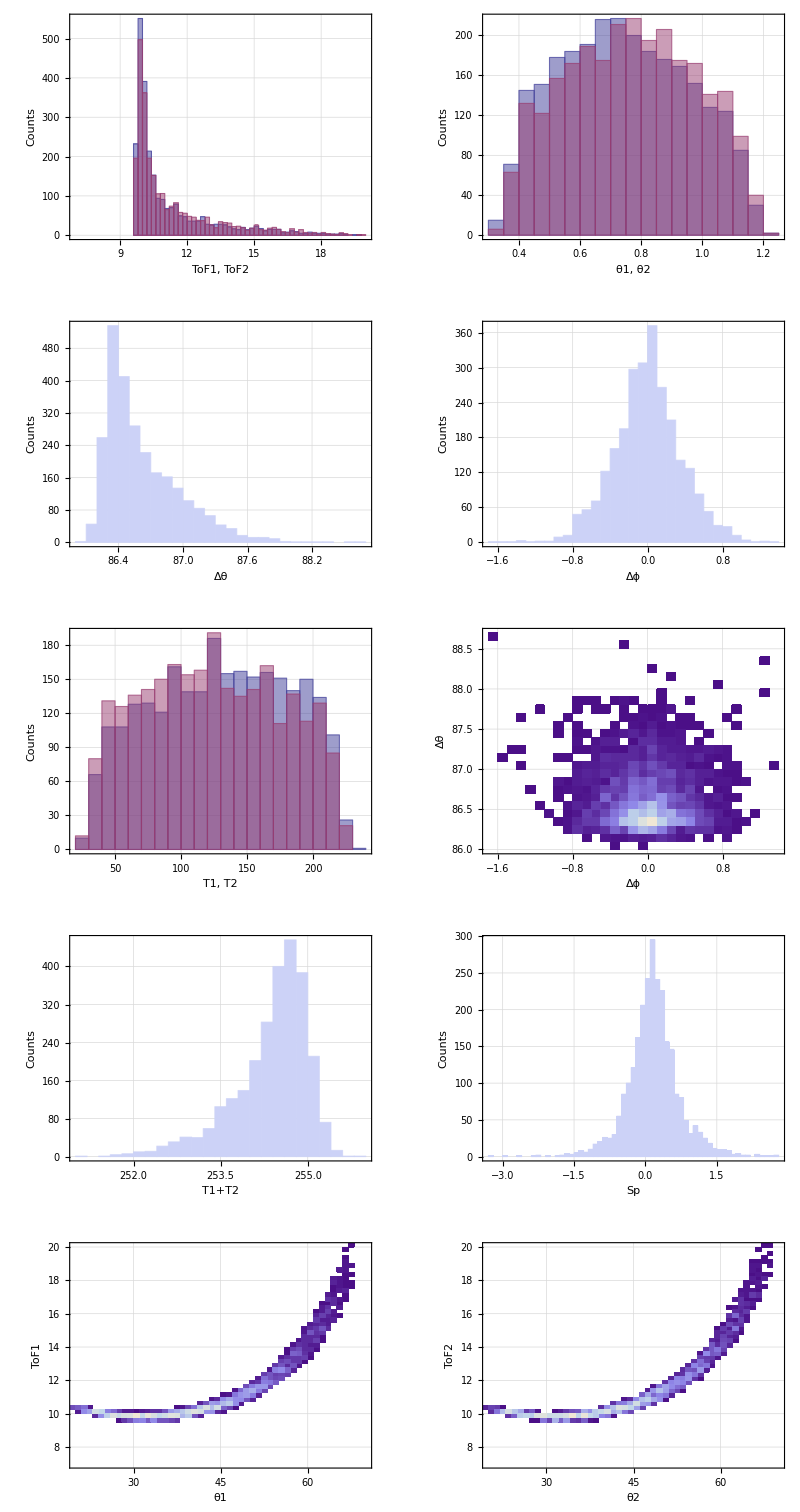

```mathematica
ObserPlots[MSObserv,m]
```

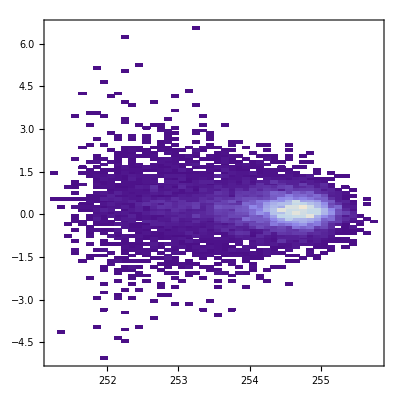

```mathematica
DensityHistogram[
Table[{MSObserv[[i,10]],MSObserv[[i,5]]},{i,1,n}]
]
```

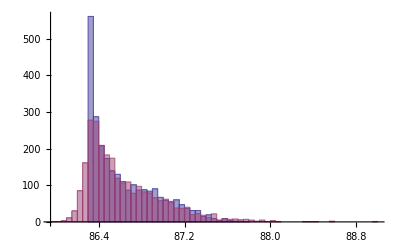

```mathematica
Histogram[{
Table[AccpP4Obser[[i,6]],{i,1,m}],
Table[MSObserv[[i,6]],{i,1,m}]
}]
```

## Detector Resolution

```mathematica
MSObserv=AccpP4Obser;
```

```mathematica
(* the change of ToF but not angle *)
σToF=0.5;
MSToF1=Table[MSObserv[[i,1]]+RandomVariate[NormalDistribution[0,σToF]],{i,1,m}];
MSToF2=Table[MSObserv[[i,2]]+RandomVariate[NormalDistribution[0,σToF]],{i,1,m}];
MWDC1=Table[Rot2.{
AccpXY[[i,1,1]]+RandomVariate[NormalDistribution[0,6]],
AccpXY[[i,1,2]]+RandomVariate[NormalDistribution[0,6]],
AccpXY[[i,1,3]]
},{i,1,m}];
MWDC2=Table[Rot1.{
AccpXY[[i,2,1]]+RandomVariate[NormalDistribution[0,6]],
AccpXY[[i,2,2]]+RandomVariate[NormalDistribution[0,6]],
AccpXY[[i,2,3]]
},{i,1,m}];
reactionPos=Table[{
0RandomVariate[NormalDistribution[0,10]],
0RandomVariate[NormalDistribution[0,10]],
0
},{i,1,m}];
FL1=Table[Norm[MWDC1[[i]]-reactionPos[[i]]] 1400/1022.37,{i,1,m}];
FL2=Table[Norm[MWDC2[[i]]-reactionPos[[i]]] 1400/1022.37,{i,1,m}];
β1=Table[FL1[[i]]/(MSToF1[[i]] c),{i,1,m}];
β2=Table[FL2[[i]]/(MSToF2[[i]]  c),{i,1,m}];
T1=Table[mp/(√(1-β1[[i]]^2))-mp,{i,1,m}];
T2=Table[mp/(√(1-β2[[i]]^2))-mp,{i,1,m}];
TotalT=Table[T1[[i]]+T2[[i]],{i,1,m}];
```

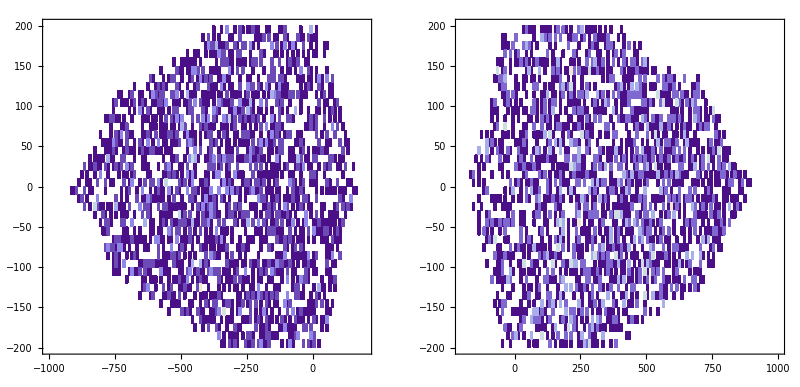

```mathematica
GraphicsGrid[{{DensityHistogram[
Table[{AccpXY[[i,1,1]],AccpXY[[i,1,2]]},{i,1,m}],{{10},{10}},PlotRange->{{-1000,200},{-200,200}}
],
DensityHistogram[
Table[{AccpXY[[i,2,1]],AccpXY[[i,2,2]]},{i,1,m}],{{10},{10}},PlotRange->{{-200,1000},{-200,200}}
]}},ImageSize->800]
```

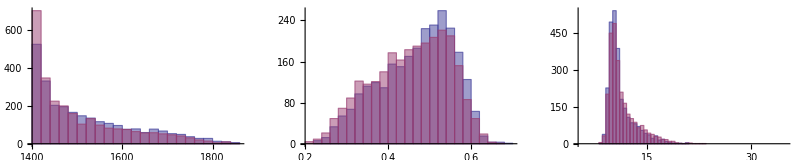

```mathematica
GraphicsGrid[{{Histogram[{FL1,FL2}],Histogram[{β1,β2}],Histogram[{MSToF1,MSToF2},{5,35,0.5}]}},ImageSize->800]
```

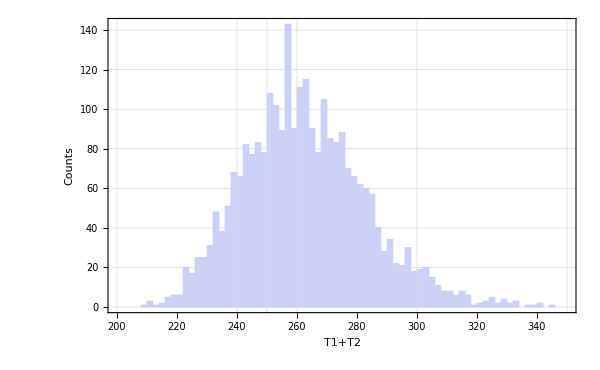

```mathematica
Histogram[TotalT,{200,350,2},ImageSize->600,GridLines->{{50,100,150,200,240,250,260,300,350,400},Automatic},Frame->True,FrameLabel->{"T1+T2","Counts"}]
```

```mathematica
Measure=Table[
{Join[{T1[[i]]+mp},√(2 mp T1[[i]]+T1[[i]]^2)Normalize[MWDC1[[i]]]],
Join[{T2[[i]]+mp},√(2 mp T2[[i]]+T2[[i]]^2)Normalize[MWDC2[[i]]]]
},{i,1,m}];
MeasureObser=Observable[Measure];
```

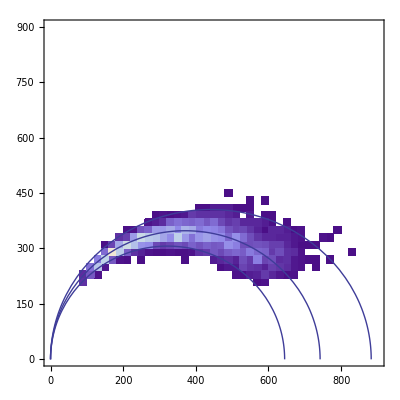

```mathematica
Show[
DensityHistogram[Table[{Measure[[i,1,4]],Norm[Measure[[i,1,2;;3]]]},{i,1,m}],{20},PlotRange->{{0,900},{0,900}}],
ParametricPlot[{√(T (2 mp+T)) Cos[(θNN °)/2]^2,(√(mp T) Sin[θNN °])/(√2)},{θNN,0,180}],
ParametricPlot[{√(200 (2 mp+200)) Cos[(θNN °)/2]^2,(√(mp 200) Sin[θNN °])/(√2)},{θNN,0,180}],
ParametricPlot[{√(350 (2 mp+350)) Cos[(θNN °)/2]^2,(√(mp 350) Sin[θNN °])/(√2)},{θNN,0,180}]
]
```

```mathematica
Table[{√(350 (2 mp+350)) Cos[(θNN °)/2]^2,(√(mp 350) Sin[θNN °])/(√2)},{θNN,36,180-36,18}]//TableForm
```

798.477 | 238.178
700.828 | 327.824
577.783 | 385.38
441.387 | 405.213
304.991 | 385.38
181.946 | 327.824
84.2974 | 238.178

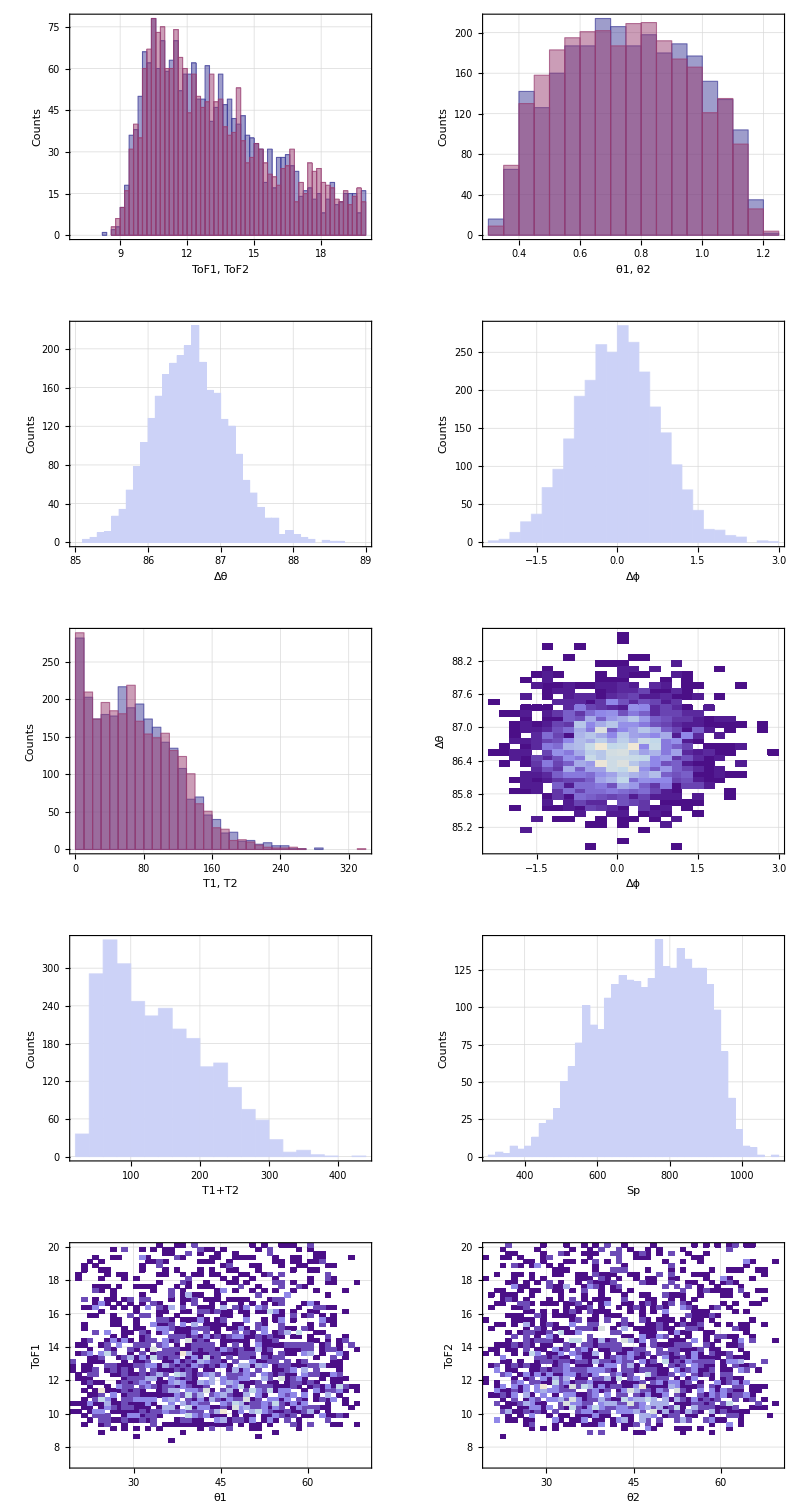

```mathematica
ObserPlots[MeasureObser,m]
```

```mathematica
MeasureObser[[1]]
```

{10.1464,11.8335,{0.141461,0.572475},{-2.98899,0.935975},923.613,86.4278,-0.638339,160.364,85.6389,246.002}

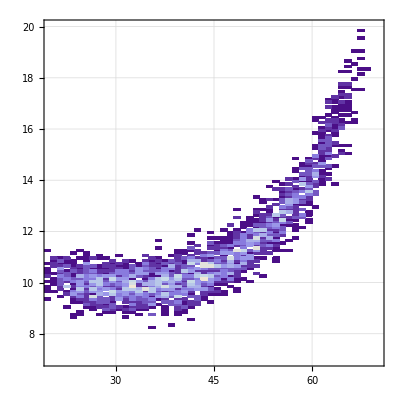

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,3,2]] 180/π,MeasureObser[[i,1]]},{i,1,m}],{{1},{0.1}}, GridLines->Automatic,PlotRange->{{20,70},{7,20}}
]
```

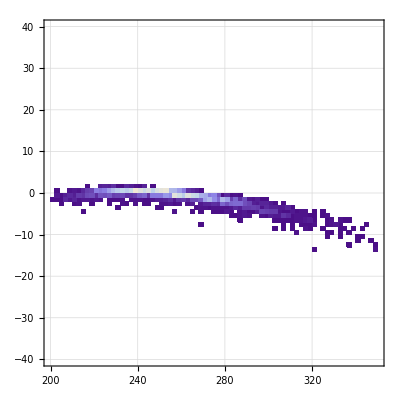

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,10]],MeasureObser[[i,5]]},{i,1,m}],{{200,350,2},{-40,40,1}},PlotRange->{{200,350},{-40,40}}, GridLines->Automatic
]
```

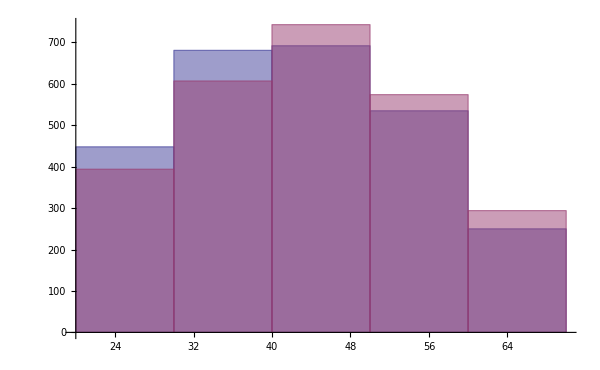

```mathematica
Asymm={Table[MeasureObser[[i,3,2]] 180/π,{i,1,m}],Table[MeasureObser[[i,4,2]] 180/π,{i,1,m}]};
Histogram[Asymm,{20,70,10},ImageSize->600]
```

```mathematica
CountL=HistogramList[Asymm[[1]],{20,70,10}][[2]]
CountR=HistogramList[Asymm[[2]],{20,70,10}][[2]]
```

{448,681,692,535,250}

{394,607,743,574,294}

```mathematica
Total[CountL]
Total[CountR]
```

2606

2612

```mathematica
Asys=Table[(CountL[[i]]-CountR[[i]])/(CountL[[i]]+CountR[[i]])//N,{i,1,5}]
```

{0.064133,0.0574534,-0.0355401,-0.0351668,-0.0808824}

```mathematica
Ay260Dist=Interpolation[
{{10.000,0.3169},
{15.000,0.3751},
{20.000,0.3723},
{25.000,0.3233},
{30.000,0.2479},
{35.000,0.1586},
{40.000,0.06205},
{45.000,-0.03654},
{50.000,-0.1323},
{55.000,-0.2207},
{60.000,-0.2971},
{65.000,-0.3545},
{70.000,-0.3805}}];
```

```mathematica
AyMean[θ_]:=1/2(Ay260Dist[θ]+Ay260Dist[θ+10])
```

```mathematica
Py=Table[Asys[[i]]/AyMean[10+10i],{i,1,5}]
DPy=Table[2/AyMean[10+10 i] √((CountL[[i]]CountR[[i]])/(CountL[[i]]+CountR[[i]])^3),{i,1,5}]
```

{0.206814,0.370727,1.01182,0.163795,0.238732}

{0.110904,0.179499,-0.751075,-0.139776,-0.126134}

```mathematica
Needs["ErrorBarPlots`"]
```

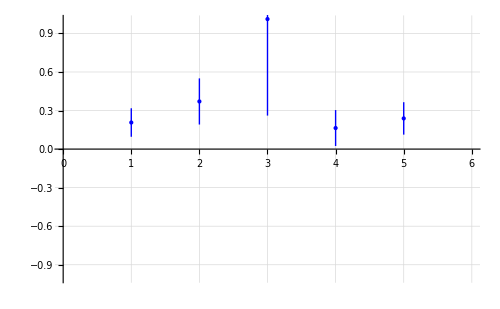

```mathematica
Table[{Py[[i]],DPy[[i]]},{i,1,5}];
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Blue,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
```